```mathematica
A={a,b,c,d}
```

{a,b,c,d}

```mathematica
FullForm[A]
```

List[a,b,c,d]

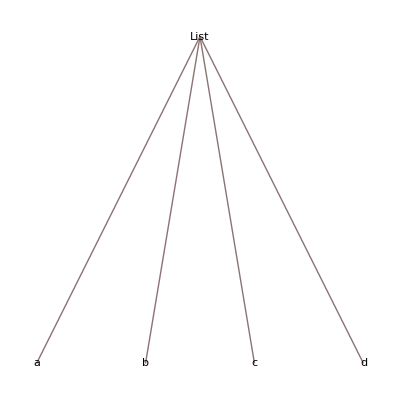

```mathematica
TreeForm[A]
```

```mathematica
Apply[f,A]
```

f[a,b,c,d]

```mathematica
Apply[f,A,{2}]
```

{a,b,c,d}

```mathematica
Map[f,A]
```

{f[a],f[b],f[c],f[d]}

```mathematica
Map[f,A,{1}]
```

{f[a],f[b],f[c],f[d]}

```mathematica
f@@A
```

f[a,b,c,d]

```mathematica
f@@@A
```

{a,b,c,d}

```mathematica
Level[a+f[x,y^n],{-2}]
```

{y^n}

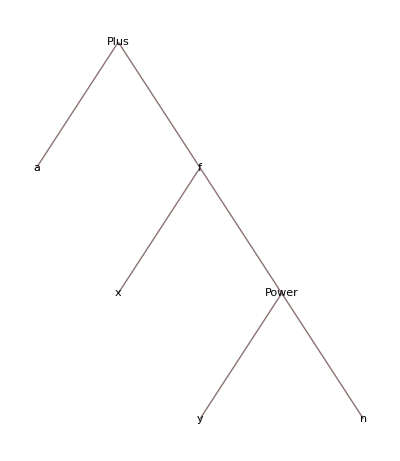

```mathematica
TreeForm[a+f[x,y^n]]
```

```mathematica
Remove["Global`*"]
```

```mathematica
(tes=Array[Random[]&,{3,3}])//MatrixForm
```

(0.12088 | 0.970395 | 0.353445
0.117701 | 0.825557 | 0.625713
0.760108 | 0.124603 | 0.563957)

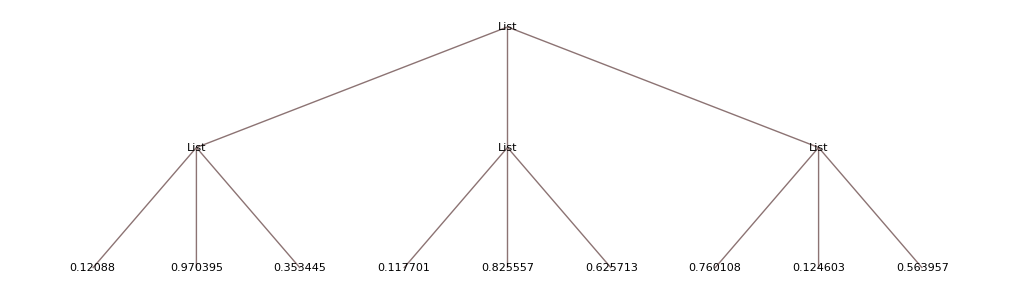

```mathematica
TreeForm[%]
```

```mathematica
MapIndexed[Delete[#1,First[#2]]&,tes]//MatrixForm
```

(0.970395 | 0.353445
0.117701 | 0.625713
0.760108 | 0.124603)

```mathematica
MapIndexed[RotateLeft[#1,#2[[1]]-1]&,tes]//MatrixForm
```

(0.12088 | 0.970395 | 0.353445
0.825557 | 0.625713 | 0.117701
0.563957 | 0.760108 | 0.124603)

```mathematica
MapIndexed[f,tes]//MatrixForm
```

(f[{0.12088,0.970395,0.353445},{1}]
f[{0.117701,0.825557,0.625713},{2}]
f[{0.760108,0.124603,0.563957},{3}])

```mathematica
Remove["Global`*"]
(m=Array[Random[]&,{3,3}])//MatrixForm
```

(0.486906 | 0.788079 | 0.405692
0.725567 | 0.384971 | 0.98158
0.00548391 | 0.567901 | 0.463745)

```mathematica
Rest[m]//MatrixForm
```

(0.725567 | 0.384971 | 0.98158
0.00548391 | 0.567901 | 0.463745)

```mathematica
MapIndexed[RotateLeft[#1,#2[[1]]-1]&,m]//MatrixForm
```

(0.486906 | 0.788079 | 0.405692
0.384971 | 0.98158 | 0.725567
0.463745 | 0.00548391 | 0.567901)

```mathematica
Transpose[{m,Range[Length[m]]}]//MatrixForm
```

({0.486906,0.788079,0.405692} | 1
{0.725567,0.384971,0.98158} | 2
{0.00548391,0.567901,0.463745} | 3)

```mathematica
Trace[Scan[If[Delete@@#=!=Array[0&,{Length[m]-1}],Return[False]]&,Transpose[{m,Range[Length[m]]}]]]
```

{{{{m,{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}}},{{{m,{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}}},Length[{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}}],3},Range[3],{1,2,3}},{{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}},{1,2,3}}},Transpose[{{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}},{1,2,3}}],{{{0.486906,0.788079,0.405692},1},{{0.725567,0.384971,0.98158},2},{{0.00548391,0.567901,0.463745},3}}},Scan[If[Delete@@#1=!=Array[0&,{Length[m]-1}],Return[False]]&,{{{0.486906,0.788079,0.405692},1},{{0.725567,0.384971,0.98158},2},{{0.00548391,0.567901,0.463745},3}}],{(If[Delete@@#1=!=Array[0&,{Length[m]-1}],Return[False]]&)[{{0.486906,0.788079,0.405692},1}],If[Delete@@{{0.486906,0.788079,0.405692},1}=!=Array[0&,{Length[m]-1}],Return[False]],{{Delete@@{{0.486906,0.788079,0.405692},1},Delete[{0.486906,0.788079,0.405692},1],{0.788079,0.405692}},{{{{{m,{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}}},Length[{{0.486906,0.788079,0.405692},{0.725567,0.384971,0.98158},{0.00548391,0.567901,0.463745}}],3},3-1,2},{2}},Array[0&,{2}],{(0&)[1],(0&)[2]},{(0&)[1],0},{(0&)[2],0},{0,0}},{0.788079,0.405692}=!={0,0},True},If[True,Return[False]],Return[False]},False}

```mathematica
Delete@@#&[Transpose[{m,Range[Length[m]]}]]
```

Delete::argt: Delete called with 3 arguments; 1 or 2 arguments are expected.

Delete[{{0.486906,0.788079,0.405692},1},{{0.725567,0.384971,0.98158},2},{{0.00548391,0.567901,0.463745},3}]

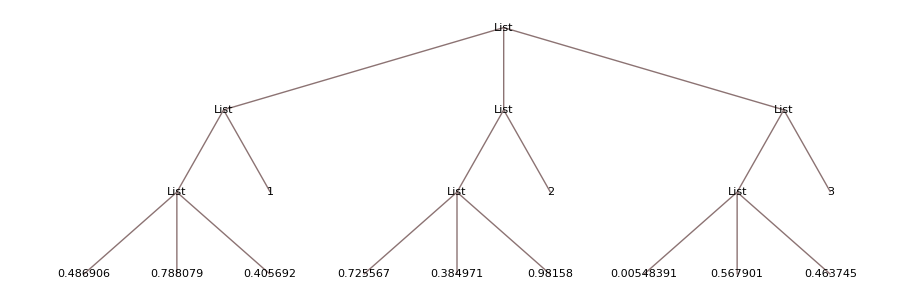

```mathematica
TreeForm[Transpose[{m,Range[Length[m]]}]]
```